```mathematica
matrixIPD = {{R,S,R},{T,P,T/m+P-c/m},{R-c/m, S/m+P(m-1)/m-c/m, R - c/m}}
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

```mathematica
R=.
```

```mathematica
MatrixForm[matrixIPD]
```

(R | S | R
T | P | -c/m+P+T/m
-c/m+R | -c/m+((-1+m) P)/m+S/m | -c/m+R)

```mathematica
ms = {x,y,z}
```

{x,y,z}

```mathematica
matrixIPD.ms
```

{R x+S y+R z,T x+P y+(-c/m+P+T/m) z,(-c/m+R) x+(-c/m+((-1+m) P)/m+S/m) y+(-c/m+R) z}

```mathematica
r = matrixIPD.ms
```

{R x+S y+R z,T x+P y+(-c/m+P+T/m) z,(-c/m+R) x+(-c/m+((-1+m) P)/m+S/m) y+(-c/m+R) z}

```mathematica
Reduce[r[[1]] == r[[2]] == r[[3]] && x+y+z==1, {x,y,z}]
```

((-1+m) (P-S) (c-m P-T+m T)≠0&&x==(-c^2-c P+c m P+m P^2-m^2 P^2-c m R-m P R+m^2 P R+c S-m P S+m^2 P S+m R S-m^2 R S+c T+P T-m P T-S T+m S T)/((-1+m) (P-S) (c-m P-T+m T))&&y==c/((-1+m) (P-S))&&z==1-x-y&&m≠0)||(m==1&&c==0&&R-S-T≠0&&y==(P-R+T-P x)/(-R+S+T)&&z==1-x-y&&P^3 R-2 P^2 R S+P R^2 S+P R S^2-R^2 S^2-P^3 T-P^2 R T-P R^2 T+2 P^2 S T+R^2 S T-P S^2 T+R S^2 T+P^2 T^2+2 P R T^2-P S T^2-2 R S T^2-P T^3+S T^3≠0)||(P==S&&c==0&&m R-m S-T≠0&&y==(m R-m S-T+m S x+T x-m T x)/(m R-m S-T)&&z==1-x-y&&-m R^2 S+m^2 R^2 S+m R^2 T-m^2 R^2 T+m R S T-m^2 R S T-2 m R T^2+2 m^2 R T^2+m T^3-m^2 T^3≠0)||(P==S&&R-S≠0&&m==T/(R-S)&&c==0&&x==0&&z==1-y&&R^3 S T-R^2 S^2 T-R^3 T^2-R^2 S T^2+R S^2 T^2+3 R^2 T^3-R S T^3-3 R T^4+S T^4+T^5≠0)||(R==T&&m==1&&c==0&&S≠0&&y==(P-P x)/S&&z==1-x-y&&P^2-P S-P T+S T≠0)||(R==T&&P==S&&c==0&&m S+T-m T≠0&&y==1-x&&z==1-x-y&&m S T≠0)||(R==T&&P==S&&S-T≠0&&m==T/(-S+T)&&c==0&&z==1-x-y&&S T≠0)||(R==S+T&&m==1&&c==0&&P≠0&&x==(P-S)/P&&z==1-x-y&&P^3 S-2 P^2 S^2+2 P S^3-S^4-P^2 S T+P S^2 T≠0)||(R==S+T&&P==S&&m==1&&c==0&&x==0&&z==1-y&&S≠0)||(S==0&&R==T&&m==1&&c==0&&x==1&&z==-y&&P^2-P T≠0)||(S==0&&R==T&&P==0&&m==1&&c==0&&z==1-x-y&&T≠0)||(T==0&&R==S&&P==S&&c==0&&x==0&&z==1-y&&-m S+m^2 S≠0)||(T==0&&S==0&&P==0&&c==0&&m R≠0&&y==1&&z==-x)||(T==0&&S==0&&R==0&&P==0&&c==0&&z==1-x-y&&m≠0)||((P==1/2 (S+T-√(-4 R S+S^2+4 R T+2 S T-3 T^2))||P==1/2 (S+T+√(-4 R S+S^2+4 R T+2 S T-3 T^2)))&&m==1&&c==0&&R-S-T≠0&&y==(P-R+T-P x)/(-R+S+T)&&z==1-x-y&&P R S+R^2 S-R S^2-2 P R T-R^2 T+R S T+P T^2+R T^2-S T^2≠0)||((P-S) (P^2-P S+R S-P T-R T+T^2)≠0&&m==(-P R+R S-R T+T^2)/(P^2-P S+R S-P T-R T+T^2)&&(-1+m) (R-T)≠0&&c==-((m P+R-m R) (P-S))/(R-T)&&y==c/((-1+m) (P-S))&&z==1-x-y&&P R-R S+R T-T^2≠0)||(P==S&&R-T≠0&&m==1&&c==0&&R-S-T≠0&&y==(R-S-T+S x)/(R-S-T)&&z==1-x-y&&R S-R T+T^2≠0)||(R==T&&P-T≠0&&m==T/(-P+T)&&c==0&&-1+m≠0&&y==0&&z==1-x&&P T-S T≠0)||(R==S+T&&(P==1/2 (S+T-√(-3 S^2+2 S T+T^2))||P==1/2 (S+T+√(-3 S^2+2 S T+T^2)))&&m==1&&c==0&&P≠0&&x==(P-S)/P&&z==1-x-y&&P-S≠0)||(S==0&&R==T&&P==0&&c==0&&-1+m≠0&&y==1-x&&z==1-x-y&&m T≠0)||(S-T≠0&&R==T^2/(-S+T)&&P==S&&c==0&&m R-m S-T≠0&&y==(m R-m S-T+m S x+T x-m T x)/(m R-m S-T)&&z==1-x-y&&m S≠0)||(S-T≠0&&R==T^2/(-S+T)&&P==0&&-S≠0&&m==1&&c==0&&S≠0&&y==T/S&&z==1-x-y)||(S-T≠0&&R==T^2/(-S+T)&&P==S&&R-S≠0&&m==T/(R-S)&&c==0&&x==0&&z==1-y&&S T≠0)||(S-T≠0&&R==T^2/(-S+T)&&S≠0&&P==0&&c==-(-1+m) T&&-(-1+m) S≠0&&y==-c/((-1+m) S)&&z==1-x-y&&m≠0)

```mathematica
14%/.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8}
```

```mathematica
Reduce[x==0.37292227050141386&&y==0.09876543209876544&&z==1-x-y &&0≤x≤1&&)
```

```mathematica
Reduce[x==0.37292227050141386&&y==0.09876543209876544&&z==1-x-y]
```

z==0.528312&&y==0.0987654&&x==0.372922

```mathematica
Reduce[0.5283122973998207 1.8928198433420367^a x^a+0.37292227050141386 2.681523950434622^a x^a+0.09876543209876544 10.125^a x^a==1]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x^a≠0&&1.89282^a==3.84174×10^-29 x^-a (4.92699×10^28-1.83738×10^28 2.68152^a x^a-4.86616×10^27 10.125^a x^a)

```mathematica
Solve[0.5283122973998207 1.8928198433420367^a x^a+0.37292227050141386 2.681523950434622^a x^a+0.09876543209876544 10.125^a x^a==1,{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1. (0.528312 1.89282^a+0.372922 2.68152^a+0.0987654 10.125^a)^(-1./a)}}

```mathematica
Manipulate[Plot[0.5283122973998207 1.8928198433420367^a x^a+0.37292227050141386 2.681523950434622^a x^a+0.09876543209876544 10.125^a x^a,{x,-8,8}],{a,-8,8}]
```

```mathematica
Reduce[r[[1]] == r[[2]] == r[[3]] && x+y+z==1, {x,y,z}]
```

((-1+m) (P-S) (c-m P-T+m T)≠0&&x==(-c^2-c P+c m P+m P^2-m^2 P^2-c m R-m P R+m^2 P R+c S-m P S+m^2 P S+m R S-m^2 R S+c T+P T-m P T-S T+m S T)/((-1+m) (P-S) (c-m P-T+m T))&&y==c/((-1+m) (P-S))&&z==1-x-y&&m≠0)||(m==1&&c==0&&R-S-T≠0&&y==(P-R+T-P x)/(-R+S+T)&&z==1-x-y&&P^3 R-2 P^2 R S+P R^2 S+P R S^2-R^2 S^2-P^3 T-P^2 R T-P R^2 T+2 P^2 S T+R^2 S T-P S^2 T+R S^2 T+P^2 T^2+2 P R T^2-P S T^2-2 R S T^2-P T^3+S T^3≠0)||(P==S&&c==0&&m R-m S-T≠0&&y==(m R-m S-T+m S x+T x-m T x)/(m R-m S-T)&&z==1-x-y&&-m R^2 S+m^2 R^2 S+m R^2 T-m^2 R^2 T+m R S T-m^2 R S T-2 m R T^2+2 m^2 R T^2+m T^3-m^2 T^3≠0)||(P==S&&R-S≠0&&m==T/(R-S)&&c==0&&x==0&&z==1-y&&R^3 S T-R^2 S^2 T-R^3 T^2-R^2 S T^2+R S^2 T^2+3 R^2 T^3-R S T^3-3 R T^4+S T^4+T^5≠0)||(R==T&&m==1&&c==0&&S≠0&&y==(P-P x)/S&&z==1-x-y&&P^2-P S-P T+S T≠0)||(R==T&&P==S&&c==0&&m S+T-m T≠0&&y==1-x&&z==1-x-y&&m S T≠0)||(R==T&&P==S&&S-T≠0&&m==T/(-S+T)&&c==0&&z==1-x-y&&S T≠0)||(R==S+T&&m==1&&c==0&&P≠0&&x==(P-S)/P&&z==1-x-y&&P^3 S-2 P^2 S^2+2 P S^3-S^4-P^2 S T+P S^2 T≠0)||(R==S+T&&P==S&&m==1&&c==0&&x==0&&z==1-y&&S≠0)||(S==0&&R==T&&m==1&&c==0&&x==1&&z==-y&&P^2-P T≠0)||(S==0&&R==T&&P==0&&m==1&&c==0&&z==1-x-y&&T≠0)||(T==0&&R==S&&P==S&&c==0&&x==0&&z==1-y&&-m S+m^2 S≠0)||(T==0&&S==0&&P==0&&c==0&&m R≠0&&y==1&&z==-x)||(T==0&&S==0&&R==0&&P==0&&c==0&&z==1-x-y&&m≠0)||((P==1/2 (S+T-√(-4 R S+S^2+4 R T+2 S T-3 T^2))||P==1/2 (S+T+√(-4 R S+S^2+4 R T+2 S T-3 T^2)))&&m==1&&c==0&&R-S-T≠0&&y==(P-R+T-P x)/(-R+S+T)&&z==1-x-y&&P R S+R^2 S-R S^2-2 P R T-R^2 T+R S T+P T^2+R T^2-S T^2≠0)||((P-S) (P^2-P S+R S-P T-R T+T^2)≠0&&m==(-P R+R S-R T+T^2)/(P^2-P S+R S-P T-R T+T^2)&&(-1+m) (R-T)≠0&&c==-((m P+R-m R) (P-S))/(R-T)&&y==c/((-1+m) (P-S))&&z==1-x-y&&P R-R S+R T-T^2≠0)||(P==S&&R-T≠0&&m==1&&c==0&&R-S-T≠0&&y==(R-S-T+S x)/(R-S-T)&&z==1-x-y&&R S-R T+T^2≠0)||(R==T&&P-T≠0&&m==T/(-P+T)&&c==0&&-1+m≠0&&y==0&&z==1-x&&P T-S T≠0)||(R==S+T&&(P==1/2 (S+T-√(-3 S^2+2 S T+T^2))||P==1/2 (S+T+√(-3 S^2+2 S T+T^2)))&&m==1&&c==0&&P≠0&&x==(P-S)/P&&z==1-x-y&&P-S≠0)||(S==0&&R==T&&P==0&&c==0&&-1+m≠0&&y==1-x&&z==1-x-y&&m T≠0)||(S-T≠0&&R==T^2/(-S+T)&&P==S&&c==0&&m R-m S-T≠0&&y==(m R-m S-T+m S x+T x-m T x)/(m R-m S-T)&&z==1-x-y&&m S≠0)||(S-T≠0&&R==T^2/(-S+T)&&P==0&&-S≠0&&m==1&&c==0&&S≠0&&y==T/S&&z==1-x-y)||(S-T≠0&&R==T^2/(-S+T)&&P==S&&R-S≠0&&m==T/(R-S)&&c==0&&x==0&&z==1-y&&S T≠0)||(S-T≠0&&R==T^2/(-S+T)&&S≠0&&P==0&&c==-(-1+m) T&&-(-1+m) S≠0&&y==-c/((-1+m) S)&&z==1-x-y&&m≠0)

```mathematica
% /. {x->x(1-p)+p(y+z)/2, y -> y(1-p)+p(x+z)/2, z-> z(1-p)+p(x+y)/2}
```

```mathematica
((-1+m) (P-S) (c-m P-T+m T)≠0&&(1-p) x+1/2 p (y+z)==(-c^2-c P+c m P+m P^2-m^2 P^2-c m R-m P R+m^2 P R+c S-m P S+m^2 P S+m R S-m^2 R S+c T+P T-m P T-S T+m S T)/((-1+m) (P-S) (c-m P-T+m T))&&(1-p) y+1/2 p (x+z)==c/((-1+m) (P-S))&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&m≠0)||(m==1&&c==0&&R-S-T≠0&&(1-p) y+1/2 p (x+z)==(P-R+T-P ((1-p) x+1/2 p (y+z)))/(-R+S+T)&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&P^3 R-2 P^2 R S+P R^2 S+P R S^2-R^2 S^2-P^3 T-P^2 R T-P R^2 T+2 P^2 S T+R^2 S T-P S^2 T+R S^2 T+P^2 T^2+2 P R T^2-P S T^2-2 R S T^2-P T^3+S T^3≠0)||(P==S&&c==0&&m R-m S-T≠0&&(1-p) y+1/2 p (x+z)==1/(m R-m S-T)(m R-m S-T+m S ((1-p) x+1/2 p (y+z))+T ((1-p) x+1/2 p (y+z))-m T ((1-p) x+1/2 p (y+z)))&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&-m R^2 S+m^2 R^2 S+m R^2 T-m^2 R^2 T+m R S T-m^2 R S T-2 m R T^2+2 m^2 R T^2+m T^3-m^2 T^3≠0)||(P==S&&R-S≠0&&m==T/(R-S)&&c==0&&(1-p) x+1/2 p (y+z)==0&&1/2 p (x+y)+(1-p) z==1-(1-p) y-1/2 p (x+z)&&R^3 S T-R^2 S^2 T-R^3 T^2-R^2 S T^2+R S^2 T^2+3 R^2 T^3-R S T^3-3 R T^4+S T^4+T^5≠0)||(R==T&&m==1&&c==0&&S≠0&&(1-p) y+1/2 p (x+z)==(P-P ((1-p) x+1/2 p (y+z)))/S&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&P^2-P S-P T+S T≠0)||(R==T&&P==S&&c==0&&m S+T-m T≠0&&(1-p) y+1/2 p (x+z)==1-(1-p) x-1/2 p (y+z)&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&m S T≠0)||(R==T&&P==S&&S-T≠0&&m==T/(-S+T)&&c==0&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&S T≠0)||(R==S+T&&m==1&&c==0&&P≠0&&(1-p) x+1/2 p (y+z)==(P-S)/P&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&P^3 S-2 P^2 S^2+2 P S^3-S^4-P^2 S T+P S^2 T≠0)||(R==S+T&&P==S&&m==1&&c==0&&(1-p) x+1/2 p (y+z)==0&&1/2 p (x+y)+(1-p) z==1-(1-p) y-1/2 p (x+z)&&S≠0)||(S==0&&R==T&&m==1&&c==0&&(1-p) x+1/2 p (y+z)==1&&1/2 p (x+y)+(1-p) z==-(1-p) y-1/2 p (x+z)&&P^2-P T≠0)||(S==0&&R==T&&P==0&&m==1&&c==0&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&T≠0)||(T==0&&R==S&&P==S&&c==0&&(1-p) x+1/2 p (y+z)==0&&1/2 p (x+y)+(1-p) z==1-(1-p) y-1/2 p (x+z)&&-m S+m^2 S≠0)||(T==0&&S==0&&P==0&&c==0&&m R≠0&&(1-p) y+1/2 p (x+z)==1&&1/2 p (x+y)+(1-p) z==-(1-p) x-1/2 p (y+z))||(T==0&&S==0&&R==0&&P==0&&c==0&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&m≠0)||((P==1/2 (S+T-√(-4 R S+S^2+4 R T+2 S T-3 T^2))||P==1/2 (S+T+√(-4 R S+S^2+4 R T+2 S T-3 T^2)))&&m==1&&c==0&&R-S-T≠0&&(1-p) y+1/2 p (x+z)==(P-R+T-P ((1-p) x+1/2 p (y+z)))/(-R+S+T)&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&P R S+R^2 S-R S^2-2 P R T-R^2 T+R S T+P T^2+R T^2-S T^2≠0)||((P-S) (P^2-P S+R S-P T-R T+T^2)≠0&&m==(-P R+R S-R T+T^2)/(P^2-P S+R S-P T-R T+T^2)&&(-1+m) (R-T)≠0&&c==-((m P+R-m R) (P-S))/(R-T)&&(1-p) y+1/2 p (x+z)==c/((-1+m) (P-S))&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&P R-R S+R T-T^2≠0)||(P==S&&R-T≠0&&m==1&&c==0&&R-S-T≠0&&(1-p) y+1/2 p (x+z)==(R-S-T+S ((1-p) x+1/2 p (y+z)))/(R-S-T)&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&R S-R T+T^2≠0)||(R==T&&P-T≠0&&m==T/(-P+T)&&c==0&&-1+m≠0&&(1-p) y+1/2 p (x+z)==0&&1/2 p (x+y)+(1-p) z==1-(1-p) x-1/2 p (y+z)&&P T-S T≠0)||(R==S+T&&(P==1/2 (S+T-√(-3 S^2+2 S T+T^2))||P==1/2 (S+T+√(-3 S^2+2 S T+T^2)))&&m==1&&c==0&&P≠0&&(1-p) x+1/2 p (y+z)==(P-S)/P&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&P-S≠0)||(S==0&&R==T&&P==0&&c==0&&-1+m≠0&&(1-p) y+1/2 p (x+z)==1-(1-p) x-1/2 p (y+z)&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&m T≠0)||(S-T≠0&&R==T^2/(-S+T)&&P==S&&c==0&&m R-m S-T≠0&&(1-p) y+1/2 p (x+z)==1/(m R-m S-T)(m R-m S-T+m S ((1-p) x+1/2 p (y+z))+T ((1-p) x+1/2 p (y+z))-m T ((1-p) x+1/2 p (y+z)))&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&m S≠0)||(S-T≠0&&R==T^2/(-S+T)&&P==0&&-S≠0&&m==1&&c==0&&S≠0&&(1-p) y+1/2 p (x+z)==T/S&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z))||(S-T≠0&&R==T^2/(-S+T)&&P==S&&R-S≠0&&m==T/(R-S)&&c==0&&(1-p) x+1/2 p (y+z)==0&&1/2 p (x+y)+(1-p) z==1-(1-p) y-1/2 p (x+z)&&S T≠0)||(S-T≠0&&R==T^2/(-S+T)&&S≠0&&P==0&&c==-(-1+m) T&&-(-1+m) S≠0&&(1-p) y+1/2 p (x+z)==-c/((-1+m) S)&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&m≠0) %/.{T-> 5, R->3,P->1,S->0.1,m->10,c->0.8}
```

```mathematica
((1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z))
```

```mathematica
(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&0≤x≤1&&0≤y≤1&&0≤z≤1
```

```mathematica
(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&0≤x≤1&&0≤y≤1&&0≤z≤1&&x+y+z==1
```

(1-p) x+1/2 p (y+z)==0.372922&&(1-p) y+1/2 p (x+z)==0.0987654&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&0≤x≤1&&0≤y≤1&&0≤z≤1&&x+y+z==1

```mathematica
NSolve[%115,{x,y,z}]
```

```mathematica
FindInstance[%115,{p,x,y,z}]
```

{{p→0.197531,x→0.389591,y→0.,z→0.610409}}

```mathematica
FindInstance[(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)&&0≤x≤1&&0≤y≤1&&0≤z≤1,{p,x,y,z}]
```

{{p→0.197531,x→0.389591,y→0.,z→0.610409}}

```mathematica
(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)
```

(1-p) x+1/2 p (y+z)==0.372922&&(1-p) y+1/2 p (x+z)==0.0987654&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)

```mathematica
Eliminate[(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z),x]
```

(-162.+243. p) y==-16.+81. p&&3401. z==2076.-2827. y

```mathematica
Solve[(-162.+243. p) y==-16.+81. p&&3401. z==2076.-2827. y,{y,z}]
```

{{y→-(16.-81. p)/(-162.+243. p),z→0.610409+(0.831226 (16.-81. p))/(-162.+243. p)}}

(-162. + 243.*p)*y == -16. + 81.*p && 3401.*z == 2076. - 2827.*y

WolframAlphaQueryResults

```mathematica
{{y->-(16.-81. p)/(-162.+243. p),z->0.6104087033225521+(0.8312261099676566 (16.-81. p))/(-162.+243. p)}}
```

{{y→-(16.-81. p)/(-162.+243. p),z→0.610409+(0.831226 (16.-81. p))/(-162.+243. p)}}

```mathematica
X==y+z/2&&Y==(√3 z)/2/.{{y->-(16.-81. p)/(-162.+243. p),z->0.6104087033225521+(0.8312261099676566 (16.-81. p))/(-162.+243. p)}}
```

```mathematica
X:=-(16.-81. p)/(-162.+243. p)+1/2 (0.6104087033225521+(0.8312261099676566 (16.-81. p))/(-162.+243. p))
Y:=1/2 √3 (0.6104087033225521+(0.8312261099676566 (16.-81. p))/(-162.+243. p))
```

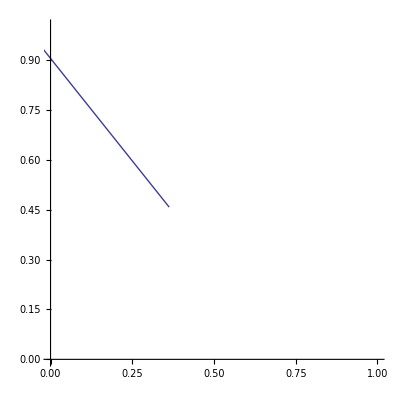

```mathematica
ParametricPlot[{X,Y},{p,0, (2/3)}, PlotRange->{{0,1},{0,1}}]
```

```mathematica
(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)
```

(1-p) x+1/2 p (y+z)==0.372922&&(1-p) y+1/2 p (x+z)==0.0987654&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z)

```mathematica
Solve[(1-p) x+1/2 p (y+z)==0.37292227050141386&&(1-p) y+1/2 p (x+z)==0.09876543209876544&&1/2 p (x+y)+(1-p) z==1-(1-p) x-(1-p) y-1/2 p (x+z)-1/2 p (y+z),{x,y,z}]
```

```mathematica
{{x->-(-0.37292227050141386+0.5 p)/(1.-1.5 p),y->-(-0.09876543209876544+0.5 p)/(1.-1.5 p),z->1.-0.4716877026001793/(1.-1.5 p)+(1. p)/(1.-1.5 p)}}
```

```mathematica
Solve[{x==-(-0.37292227050141386+0.5 p)/(1.-1.5 p),y==-(-0.09876543209876544+0.5 p)/(1.-1.5 p),z==1.-0.4716877026001793/(1.-1.5 p)+(1. p)/(1.-1.5 p),x≥0,y≥0,z≥0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
{z->ConditionalExpression[(-15320.+(14499. (-4.06054573785*^11+1.088845064788*^12 x))/(-5.44422532394*^11+1.633267597182*^12 x))/(-28998.+(43497. (-4.06054573785*^11+1.088845064788*^12 x))/(-5.44422532394*^11+1.633267597182*^12 x)),0.2656526353024409<x<0.38959129667744774],y->ConditionalExpression[(-16.+(81. (-4.06054573785*^11+1.088845064788*^12 x))/(-5.44422532394*^11+1.633267597182*^12 x))/(-162.+(243. (-4.06054573785*^11+1.088845064788*^12 x))/(-5.44422532394*^11+1.633267597182*^12 x)),0.2656526353024409<x<0.38959129667744774],p->ConditionalExpression[(-4.06054573785*^11+1.088845064788*^12 x)/(-5.44422532394*^11+1.633267597182*^12 x),0.2656526353024409<x<0.38959129667744774]}
```

{z→ConditionalExpression[(-15320.+(14499. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x))/(-28998.+(43497. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x)),0.265653<x<0.389591],y→ConditionalExpression[(-16.+(81. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x))/(-162.+(243. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x)),0.265653<x<0.389591],p→ConditionalExpression[(-4.06055×10^11+1.08885×10^12 x)/(-5.44423×10^11+1.63327×10^12 x),0.265653<x<0.389591]}

```mathematica
First[%106]
```

{z→ConditionalExpression[(-15320.+(14499. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x))/(-28998.+(43497. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x)),0.265653<x<0.389591],y→ConditionalExpression[(-16.+(81. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x))/(-162.+(243. (-4.06055×10^11+1.08885×10^12 x))/(-5.44423×10^11+1.63327×10^12 x)),0.265653<x<0.389591],p→ConditionalExpression[(-4.06055×10^11+1.08885×10^12 x)/(-5.44423×10^11+1.63327×10^12 x),0.265653<x<0.389591]}

```mathematica
matrixIPD
```

{{R,S,R},{T,P,-c/m+P+T/m},{-c/m+R,-c/m+((-1+m) P)/m+S/m,-c/m+R}}

```mathematica
x
```

x

```mathematica
x={x1,x2,x3}
```

```mathematica
{x1,x2,x3}
i = {1,2,3}
```

{x1,x2,x3}

```mathematica
R=.
```

```mathematica
R
```

R

```mathematica
R = matrixIPD.x
```

matrixIPD.x